```mathematica
DSolve[{D[x[t], t]==-a y[t],D[y[t], t]==-b x[t],x[0]==c,y[0]==d},{x[t],y[t]},t]
```

{{x[t]→(ⅇ^(-√a √b t) (√b c+√a d+√b c ⅇ^(2 √a √b t)-√a d ⅇ^(2 √a √b t)))/(2 √b),y[t]→(ⅇ^(-√a √b t) (√b c+√a d-√b c ⅇ^(2 √a √b t)+√a d ⅇ^(2 √a √b t)))/(2 √a)}}

```mathematica
Plot[{ⅇ^(-0.01414213562373095 t) (65355.339059327365-5355.339059327365 ⅇ^(0.0282842712474619 t)),ⅇ^(-0.01414213562373095 t) (46213.20343559643+3786.7965644035685 ⅇ^(0.0282842712474619 t))},{t,0,7}]
```

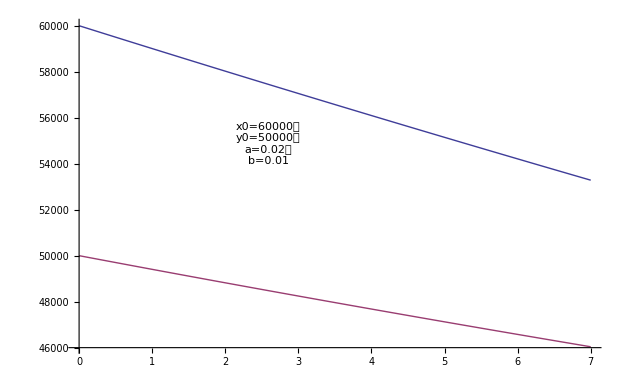
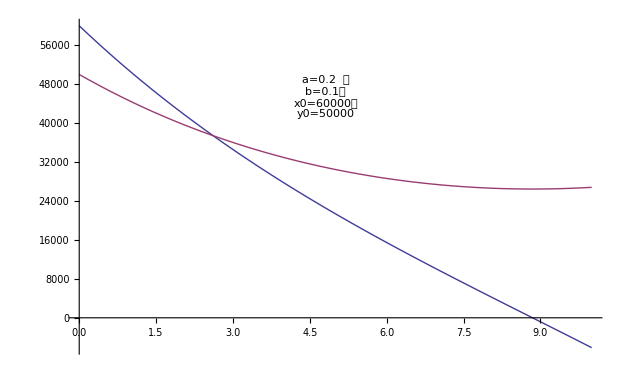

```mathematica
DSolve[{D[y[x], x]== x/y[x],D[y1[x], x]== x/y1[x],D[y2[x], x]== x/y2[x],y[0]==8,y1[0]==6,y2[0]==5},{y[x],y1[x],y2[x]},x]
```

```mathematica
m={8,7,6,5,4,3,2,1}
```

{8,7,6,5,4,3,2,1}

```mathematica
DSolve[{D[y[x], x]== (2x)/y[x],y[0]==7},y[x],x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{y[x]→√(49+2 x^2)}}

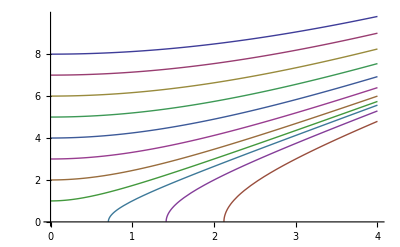

```mathematica
Plot[{√(64+2 x^2),√(49+2 x^2),√(36+2x^2),√(25+2x^2),√(16+2x^2),√(9+2x^2),√(4+2x^2),√(1+2x^2),√(-1+2x^2),√(-4+2x^2),√(-9+2x^2)},{x,0,4}]
```

```mathematica
20000^2 0.0544-0.0106 50000^2
```

-4.74×10^6

```mathematica
√(0.0106 50000^2÷0.0544)
```

22071.1

```mathematica
5000^2 0.0000025-0.2 312
```

0.1

```mathematica
50000^2 0.0000025/0.2
```

31250.

```mathematica
m={{-0.001,-0.1},{-0.1,-0.001}}
```

```mathematica
{{-0.001,-0.1},{-0.1,-0.001}}
Eigensystem[m]
```

{{-0.001,-0.1},{-0.1,-0.001}}

{{-0.101,0.099},{{0.707107,0.707107},{-0.707107,0.707107}}}

```mathematica
m={{-0.00001,-0.1},{-0.1,-0.0001}}
```

{{-0.00001,-0.1},{-0.1,-0.0001}}

```mathematica
Eigensystem[m]
```

{{-0.100055,0.099945},{{0.706948,0.707266},{-0.707266,0.706948}}}